```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
L1=1;
```

```mathematica
ap1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
mpd=I*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
mpu=I*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
dp1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
ep1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
fp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
gp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
rsp1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
rsp1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
tup1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
tup1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
d=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-d-L1-zero.wdx"];
df1n=Query[1]@d;
dlf1n=Interpolation[Flatten[df1n,1]];
dsf1[x_,t_]=dlf1n[x,t];

dg1n=Query[1]@d;
```

```mathematica
e=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-e-L1-zero.wdx"];
ef1n=Query[1]@e;
elf1n=Interpolation[Flatten[ef1n,1]];
esf1[x_,t_]=elf1n[x,t];

eg1n=Query[1]@e;
```

```mathematica
f=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-f-L1-zero.wdx"];
ff1n=Query[1]@f;
flf1n=Interpolation[Flatten[ff1n,1]];
fsf1[x_,t_]=flf1n[x,t];

fg1n=Query[2]@f;
flg1n=Interpolation[Flatten[fg1n,1]];
fsg1[x_,t_]=flg1n[x,t];
```

```mathematica
g=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-g-L1-zero.wdx"];
gf1n=Query[1]@g;
glf1n=Interpolation[Flatten[gf1n,1]];
gsf1[x_,t_]=glf1n[x,t];

gg1n=Query[2]@g;
glg1n=Interpolation[Flatten[gg1n,1]];
gsg1[x_,t_]=glg1n[x,t];
```

```mathematica
rs=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-rs-L1-zero.wdx"];
rsf1n=Query[1]@rs;
rslf1n=Interpolation[Flatten[rsf1n,1]];
rssf1[x_,t_]=rslf1n[x,t];

rsg1n=Query[2]@rs;
rslg1n=Interpolation[Flatten[rsg1n,1]];
rssg1[x_,t_]=rslg1n[x,t];
```

```mathematica
tu=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-tu-L1-zero.wdx"];
tuf1n=Query[1]@tu;
tulf1n=Interpolation[Flatten[tuf1n,1]];
tusf1[x_,t_]=tulf1n[x,t];

tug1n=Query[2]@tu;
tulg1n=Interpolation[Flatten[tug1n,1]];
tusg1[x_,t_]=tulg1n[x,t];
```

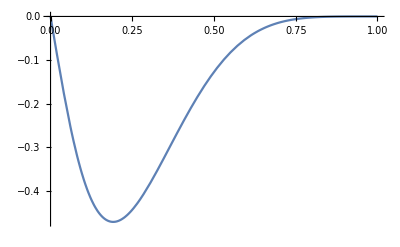
-Graphics-d+ef

```mathematica
de=Labeled[Plot[dp1*dsf1[x,0]+ep1*esf1[x,0],{x,0,1}],{"d+e","f"},{Left,Top}]
```

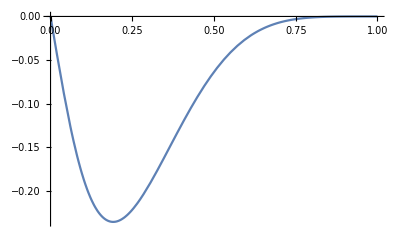

```mathematica
Plot[ep1*esf1[x,0],{x,0,1}]
```

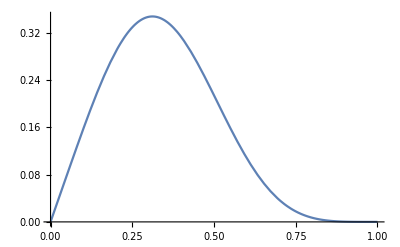
-Graphics-f+gf

```mathematica
fg=Labeled[Plot[fp1*fsf1[x,0]+gp1*gsf1[x,0],{x,0,1}],{"f+g","f"},{Left,Top}]
```

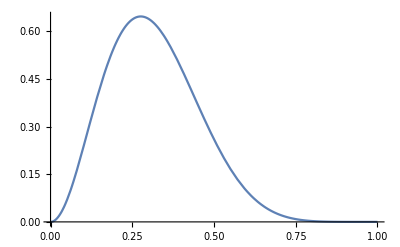
-Graphics-f+gg

```mathematica
fg2=Labeled[Plot[fp1*fsg1[x,0]+gp1*gsg1[x,0],{x,0,1}],{"f+g","g"},{Left,Top}]
```

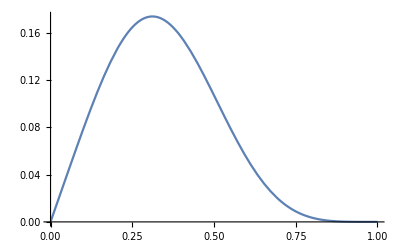

```mathematica
Plot[gp1*gsf1[x,0],{x,0,1}]
```

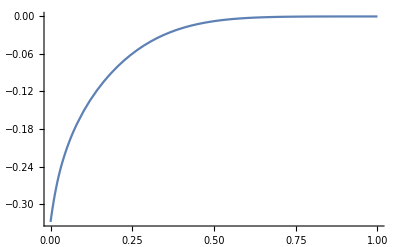
-Graphics-r+sf

```mathematica
rs=Labeled[Plot[rsp1d*rssf1[x,0],{x,0,1},PlotRange->All],{"r+s","f"},{Left,Top}]
```

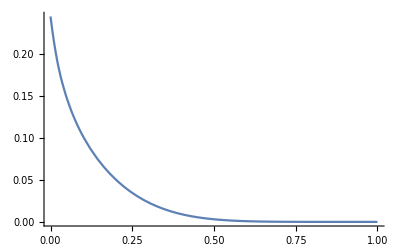
-Graphics-r+sg

```mathematica
rs2=Labeled[Plot[rsp1d*rssg1[x,0],{x,0,1},PlotRange->All],{"r+s","g"},{Left,Top}]
```

```mathematica
rssf1[0,0]
```

0.-23.0047 ⅈ

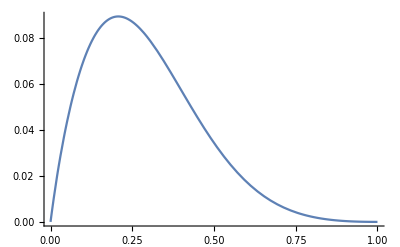
-Graphics-t+uf

```mathematica
tu=Labeled[Plot[tup1d*tusf1[x,0],{x,0,1},PlotRange->All],{"t+u","f"},{Left,Top}]
```

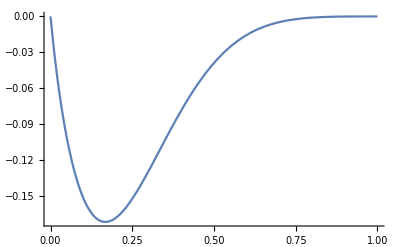
-Graphics-t+ug

```mathematica
tu2=Labeled[Plot[tup1d*tusg1[x,0],{x,0,1},PlotRange->All],{"t+u","g"},{Left,Top}]
```

```mathematica
pathde=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"de.pdf"}];
pathfg=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"fg.pdf"}];
pathrs=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"rs.pdf"}];
pathtu=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"tu.pdf"}];
```

```mathematica
pathfg2=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"fg2.pdf"}];
pathrs2=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"rs2.pdf"}];
pathtu2=FileNameJoin[{"G:\\output\\summary\\gpd\\zero\\106",
"tu2.pdf"}];
```

```mathematica
Export[pathde,de]
```

G:\output\summary\gpd\zero\106\de.pdf

```mathematica
ExpandFileName["G:\\output\\summary\\gpd\\zero\\106\\de.pdf"]
```

G:\output\summary\gpd\zero\106\de.pdf

```mathematica
Export[pathfg,fg]
```

G:\output\summary\gpd\zero\106\fg.pdf

```mathematica
Export[pathfg2,fg2]
```

G:\output\summary\gpd\zero\106\fg2.pdf

```mathematica
Export[pathrs,rs]
```

G:\output\summary\gpd\zero\106\rs.pdf

```mathematica
Export[pathrs2,rs2]
```

G:\output\summary\gpd\zero\106\rs2.pdf

```mathematica
Export[pathtu,tu]
```

G:\output\summary\gpd\zero\106\tu.pdf

```mathematica
Export[pathtu2,tu2]
```

G:\output\summary\gpd\zero\106\tu2.pdf